```mathematica
ClearAll["Global`*"];
ClearAll[m];
(*参数parameters*)
a=2/10;
Qm=5/10;
```

```mathematica
(*度规Metric*)
m[r_]:=1-Qm^2/(2r);
Σ=r^2+a^2 Cos[θ]^2;
Δ=r^2-2 m[r]r+a^2;
g={{-(1-(2 m[r]r)/Σ),0,0,-(1/Σ)2 a m[r]r Sin[θ]^2},{0,Σ/Δ,0,0},{0,0,Σ,0},{-(1/Σ)2 a m[r]r Sin[θ]^2,0,0,(r^2+a^2+(1/Σ)2 m[r] a^2 r Sin[θ]^2)Sin[θ]^2}};(*g_{\mu\nu}*)
Ig={{(-((a^2+r^2)^2-a^2 (a^2-2 m[r]r+r^2) Sin[θ]^2))/((r^2+a^2 Cos[θ]^2)(a^2-2 m[r]r+r^2)),0,0,-(2 a m[r]r)/((r^2+a^2 Cos[θ]^2)(a^2-2 m[r]r+r^2))},{0,(a^2-2 m[r]r+r^2)/(r^2+a^2 Cos[θ]^2),0,0},{0,0,1/(r^2+a^2 Cos[θ]^2),0},{-(2 a m[r]r)/((r^2+a^2 Cos[θ]^2)(a^2-2 m[r]r+r^2)),0,0,((a^2-2 m[r]r+r^2)-a^2 Sin[θ]^2)/((r^2+a^2 Cos[θ]^2)(a^2-2 m[r]r+r^2)Sin[θ]^2)}};(*g^{\mu\nu}*)
(*哈密顿量Hamiltonian*)
QQ={qt,qr,qθ,qϕ};
H=1/2(Sum[Ig[[i,j]]QQ[[i]]QQ[[j]],{i,1,4},{j,1,4}])//Simplify;
(*运动方程EoM*)
du={td,rd,θd,ϕd,qrd,qθd};
td=D[H,qt];
rd=D[H,qr];
θd=D[H,qθ];
ϕd=D[H,qϕ];
qrd=-D[H,r];
qθd=-D[H,θ];
Deom=du/.{qt->-EE,qϕ-> LL,t-> t[λ],r-> r[λ],θ-> θ[λ],ϕ-> ϕ[λ],qr-> qr[λ],qθ-> qθ[λ]};
(*\delta*)
Print["-------------------------------Done 1-------------------------------------------"]
```

-------------------------------Done 1-------------------------------------------

```mathematica
(*定义Kerr度规*)
ClearAll[MetricDown];
MetricDown[{t_,r_,θ_,ϕ_}]:=Module[{tt,rr,θθ,ϕϕ,tϕ,Σ,Δ},
Σ=r^2+a^2 Cos[θ]^2;
Δ=r^2-2m[r] r+a^2;
tt=-(1-(2 m[r] r)/Σ);
rr=Σ/Δ;
θθ=Σ;
ϕϕ=(r^2+a^2+(2 m[r] a^2 r Sin[θ]^2)/Σ)Sin[θ]^2;
tϕ=-(2 a m[r]r Sin[θ]^2)/Σ;
({{tt, 0, 0, tϕ}, {0, rr, 0, 0}, {0, 0, θθ, 0}, {tϕ, 0, 0, ϕϕ}})];
(*把θ变到0~π，把ψ变到0~2π*)
ClearAll[WrapAngle];
WrapAngle[a1_,a2_]:=Module[{x1=a1,x2=a2},
While[x1>π,x1=x1-2π];
While[x1<-π,x1=x1+2π];
If[x1<0,x1=-x1;x2=x2+π];
While[x2≥2π,x2=x2-2π];
While[x2<0,x2=x2+2π];
{x1,x2}];
(*ZAMO标架场*)
ClearAll[LocalTetrads];
LocalTetrads[pos_,metric_]:=Module[{e0,e1,e2,e3,gtt,grr,gθθ,gϕϕ,gtϕ},
{gtt,grr,gθθ,gϕϕ,gtϕ}=Extract[metric,{{1,1},{2,2},{3,3},{4,4},{1,4}}];
e0=√(-(gϕϕ/(gtt gϕϕ-gtϕ gtϕ))){1,0,0,-(gtϕ/gϕϕ)};(*Subscript[e, t]*)
e1={0,-(1/(√grr)),0,0};(*-Subscript[e, r]*)
e2={0,0,1/(√gθθ),0};(*Subscript[e, θ]*)
e3={0,0,0,-(1/(√gϕϕ))};(*-Subscript[e, ϕ]*)
{e0,e1,e2,e3}];
(*得到光线的初始方向以及相对应的上标四速度*)
ClearAll[GetIniMomentum];
GetIniMomentum[metric_,pos_,fov_,npix_][i_,j_]:=Module[{λdot,xscr,yscr,θx,ψx,vel,e0,e1,e2,e3,momentum,IKn},
{xscr,yscr}=(2Tan[fov/2]/npix)(#-(1/2)(npix+1))&/@{i,j};
{θx,ψx}=WrapAngle[2ArcTan[(√(xscr^2+yscr^2))/2],ArcTan[-yscr,-xscr]];
vel=N@{Cos[θx],Sin[θx]Cos[ψx],Sin[θx]Sin[ψx]};
{e0,e1,e2,e3}=N@LocalTetrads[pos,metric];
λdot=e0-(vel[[1]]e1+vel[[2]]e2+vel[[3]]e3);
momentum=metric.λdot;
momentum];
(*数值求解单条光线的方程*)
ClearAll[TraceSingleRay];
TraceSingleRay[pos_,fov_,npix_][i_,j_]:=Module[{λF=3000,eqns,E0,L0,idata,initialConditions,sol,frame,momentum,eom,data,tag,rF,delta},
momentum=GetIniMomentum[MetricDown[pos],pos,fov,npix][i,j];
{E0,L0}={-momentum[[1]],momentum[[4]]};
idata=Join[pos,{momentum[[2]],momentum[[3]]}];
initialConditions=Thread[{t[0],r[0],θ[0],ϕ[0],qr[0],qθ[0]}==idata];
eom=Thread[{t'[λ],r'[λ],θ'[λ],ϕ'[λ],qr'[λ],qθ'[λ]}==Deom];
eqns=N[Join[eom,initialConditions]/.{EE-> E0,LL-> L0}];
sol=NDSolve[eqns,{t,r,θ,ϕ,qr,qθ},{λ,0,-λF},Method->{"EventLocator", "Event"->{r[λ]-1.01horizon,r[λ]-10000horizon},"EventAction":>{Throw[λF =-λ,"StopIntegration"],Throw[λF =-λ,"StopIntegration"]}}];
rF=r[-λF]/.sol[[1]];
{r[-λF],θ[-λF],ϕ[-λF],qr[-λF],qθ[-λF],E0,L0}/.sol[[1]]]
(*搞一个进度条查看跑了多少*)
ClearAll[MonitorParallelTable];
MonitorParallelTable[expr_,npix_]:= Module[{res,iterCount=npix^2,progress=0},
  SetSharedVariable[progress];
  res=Monitor[ParallelTable[(progress++;expr[j,i]),{i,1,npix},{j,1,npix}],
(*i对应行,画图时是y坐标,j对应列,画图时是x坐标。但是TraceSingleRay的参数中,第一个元素是x坐标,第二个元素是y坐标,所以看起来有点奇怪*)
    Column[{ToString@progress<>" of "<>ToString@iterCount,ProgressIndicator[progress,{0,iterCount}]},Alignment->Center]];
  UnsetShared[progress];
res];
(*跑所有的点*)
ClearAll[TraceRay];
TraceRay[pos_,fov_,npix_]:=MonitorParallelTable[TraceSingleRay[pos,fov,npix],npix];
Print["-------------------------------Done 2-------------------------------------------"]
```

-------------------------------Done 2-------------------------------------------

```mathematica
(*准备就绪，开始跑函数*)
ClearAll[result,resultplot]
horizon=1+Sqrt[1-a^2-Qm^2];
pos={0,80,π/2-0.01,0};
fov=π/5;
npix=256;(*should be even*)
result=TraceRay[pos,fov,npix];
resultplot=result[[All,All,1;;3]];
```

```mathematica
(*验证一下末态哈密顿量*)
icheck=100;(*检查点(icheck,icheck)的哈密顿量是否为0*)
Print[H/.{r->result[[icheck,icheck,1]],θ->result[[icheck,icheck,2]],qr->result[[icheck,icheck,4]],qθ->result[[icheck,icheck,5]],qt->-result[[icheck,icheck,6]],qϕ->result[[icheck,icheck,7]]}];
```

-2.94049×10^-7

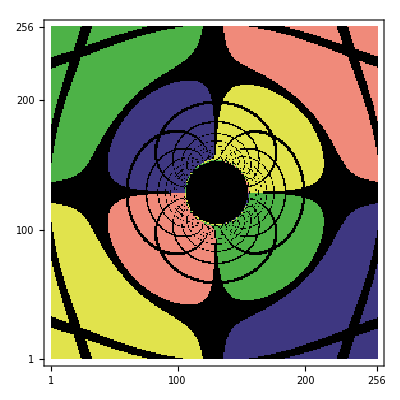

-Graphics-

```mathematica
split=π/18;
ClearAll[GetColor];
ClearAll[GetClosestAngle];
{θ0,ϕ0}={pos[[3]],pos[[4]]};
GetClosestAngle[x_]:=With[{q=IntegerPart[x/split]},Min[(q+1)split-x,x-q split]];
GetColor[{rF_,θFx_,ϕFx_}]:=Module[{θF,ϕF},
If[rF<3 horizon,Return[Black]];(*此处原本是rF<1.1 horizon0,但好像违反这个条件不足以保证光子可以出射*)
{θF,ϕF}={θFx,ϕFx};
{n1,n2}={Sin[θF] Sin[ϕF-ϕ0],-Cos[θ0]Sin[θF] Cos[ϕF-ϕ0]+Sin[θ0]Cos[θF]};
{theta,psi}=WrapAngle[ArcSin[n2],ArcSin[n1]];(*注意theta和psi都是纬线*)
Which[GetClosestAngle[theta]≤0.01||GetClosestAngle[psi]≤0.01,Return[Black],n1>0&&n2>0,RGBColor[{240,138,122}/255](*red*),n1>0&&n2<0,RGBColor[{62,55,129}/255](*blue*),n1<0&&n2< 0,RGBColor[{225,227,76}/255](*yellow*),n1<0&&n2>0,RGBColor[{77,178,71}/255](*green*)]];
MatrixPlot[Map[GetColor,resultplot,{2}],DataReversed->{True,False},AspectRatio->1]
(*画Shadow*)
MatrixPlot[Map[If[#<3horizon,1,0]&,resultplot⟦All,All,1⟧,{2}],ColorFunction->"Monochrome",DataReversed->{True,False},AspectRatio->1]
```